# La cuenta y el aro

## Diagrama de bifurcación

```mathematica
branch1=ParallelTable[{g,ϕ/.FindRoot[Cos[ϕ]==1/g,{ϕ,Pi/2}]},{g,1.001,5,0.001}];
branch2=ParallelTable[{g,ϕ/.FindRoot[Cos[ϕ]==1/g,{ϕ,-Pi/2}]},{g,1.001,5,0.001}];
```

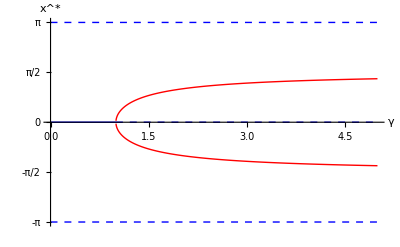

```mathematica
Show[Plot[Pi,{r,0,5},PlotStyle->{Blue,Dashed,Thick},AxesLabel->{γ,SuperStar[x]},PlotRange->{{0,5},{-Pi,Pi}},Ticks->{Automatic,{-Pi,-Pi/2,0,Pi/2,Pi}}],Plot[0,{r,0,1},PlotStyle->{Blue,Thick}],Plot[-Pi,{r,0,5},PlotStyle->{Blue,Dashed,Thick}],Plot[0,{r,1,5},PlotStyle->{Blue,Thick,Dashed}],ListPlot[branch1,Joined->True,PlotStyle->{Red,Thick}],ListPlot[branch2,Joined->True,PlotStyle->{Red,Thick}]]
```

## Espacios de fase bidimensionales

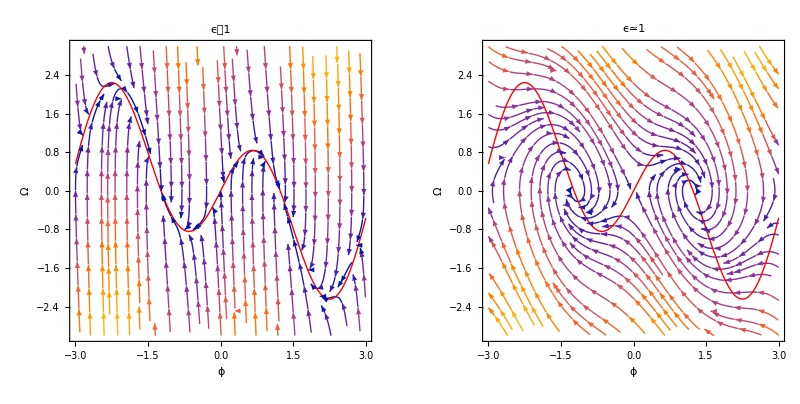

```mathematica
GraphicsRow[{Show[{StreamPlot[{y,(Sin[x]*(3*Cos[x]-1)-y)/0.05},{x,-3,3},{y,-3,3},FrameLabel->{ϕ,Ω},PlotLabel->ϵ⪡1],Plot[Sin[x]*(3*Cos[x]-1),{x,-3,3},PlotStyle->{Red,Thick}]}],Show[{StreamPlot[{y,(Sin[x]*(3*Cos[x]-1)-y)},{x,-3,3},{y,-3,3},FrameLabel->{ϕ,Ω},PlotLabel->ϵ≃1],Plot[Sin[x]*(3*Cos[x]-1),{x,-3,3},PlotStyle->{Red,Thick}]}]}]
```